```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
FileNames[]
```

{1200.nb,1200_upravene.nb,1400.nb,1500.nb,1600.nb,1800.nb,2000.nb,final-NG-1200-100SK-27BTDC.pdf,NG-1200-100SK-27BTDC.TXT,NG-1400-100SK-27BTDC.TXT,NG-1500-100SK-27BTDC.TXT,NG-1600-100SK-27BTDC.TXT,NG-1800-100SK-27BTDC.TXT,NG-2000-100SK-27BTDC.TXT,piatystlpec-NG-1200-100SK-27BTDC.TXT.txt,piatystlpec-NG-1200-100SK-27BTDC.TXT.xls,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.txt,stvrtystlpec-NG-1200-100SK-27BTDC.TXT.xls,tretistlpec-NG-1200-100SK-27BTDC.TXT.txt,tretistlpec-NG-1200-100SK-27BTDC.TXT.xls}

```mathematica
sub="NG-1600-100SK-27BTDC.TXT";
```

```mathematica
g=ReadList[sub,Table[Number,{5}]];
```

```mathematica
prvystlpec=g[[All,1]];
druhystlpec=g[[All,2]];
tretistlpec=g[[All,3]];
stvrtystlpec=g[[All,4]];
piatystlpec=g[[All,5]];
```

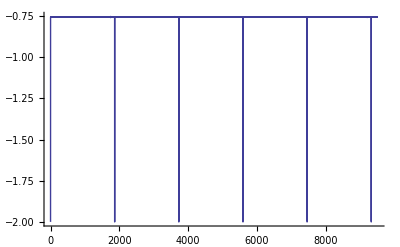

```mathematica
ListLinePlot[druhystlpec[[1;;9500;;1]],PlotRange->All]
```

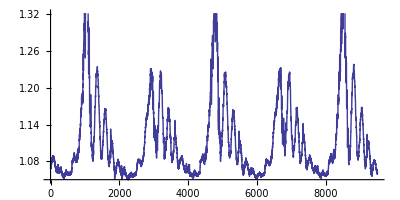

```mathematica
ListLinePlot[tretistlpec[[1;;9500;;1]],AspectRatio->0.5]
```

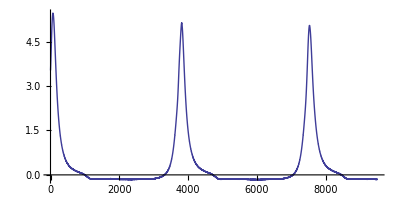

```mathematica
ListLinePlot[stvrtystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

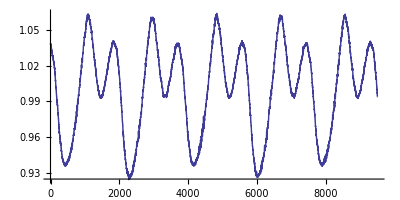

```mathematica
ListLinePlot[piatystlpec[[1;;9500;;1]], PlotRange->All,AspectRatio->0.5]
```

```mathematica
Length[prvystlpec]
```

1045976

```mathematica
pom3={};
Do[
If[druhystlpec[[i]]<-1.8,AppendTo[pom3, i]],{i,1,Length[druhystlpec]}];
pom4={};
Do[
If[pom3[[i+1]]-pom3[[i]]>10,AppendTo[pom4,pom3[[i]]]],{i,1, Length[pom3]-1}];
pom4
```

{1,1865,3729,5593,7457,9320,11185,13049,14914,16778,18642,20506,22371,24234,26098,27962,29826,31689,33553,35417,37280,39143,41007,42871,44735,46598,48462,50325,52189,54052,55915,57779,59642,61506,63370,65234,67098,68963,70827,72691,74556,76420,78284,80148,82012,83876,85741,87605,89470,91334,93199,95063,96928,98793,100657,102522,104386,106250,108114,109978,111842,113706,115570,117433,119297,121161,123025,124889,126753,128616,130480,132344,134208,136072,137937,139800,141664,143528,145392,147257,149120,150984,152849,154713,156577,158441,160305,162168,164032,165896,167759,169623,171486,173349,175213,177076,178939,180802,182666,184529,186393,188256,190120,191984,193848,195712,197576,199439,201303,203166,205030,206894,208758,210621,212485,214349,216213,218076,219940,221804,223668,225532,227396,229260,231124,232988,234853,236718,238583,240448,242312,244177,246042,247907,249771,251635,253500,255364,257228,259093,260957,262821,264685,266549,268413,270278,272142,274006,275870,277734,279599,281463,283328,285192,287056,288920,290784,292648,294513,296377,298241,300106,301971,303836,305700,307564,309429,311293,313157,315021,316886,318750,320615,322480,324344,326209,328074,329938,331804,333668,335532,337396,339260,341124,342988,344852,346716,348580,350444,352308,354173,356036,357901,359764,361628,363492,365357,367222,369087,370950,372814,374678,376543,378407,380271,382134,383998,385862,387725,389589,391453,393317,395180,397044,398907,400770,402634,404497,406361,408225,410089,411952,413816,415680,417544,419408,421273,423137,425001,426866,428730,430595,432459,434324,436187,438051,439916,441780,443644,445509,447373,449237,451101,452965,454829,456692,458556,460419,462283,464146,466009,467872,469736,471599,473462,475325,477188,479052,480915,482779,484642,486506,488370,490233,492097,493960,495823,497687,499550,501413,503276,505139,507003,508866,510730,512593,514457,516320,518184,520048,521911,523775,525639,527503,529367,531231,533096,534960,536824,538688,540553,542417,544282,546146,548011,549875,551740,553604,555469,557333,559198,561062,562926,564791,566656,568522,570388,572252,574118,575982,577848,579713,581578,583443,585308,587174,589039,590904,592768,594633,596497,598362,600226,602090,603954,605818,607682,609545,611409,613273,615137,617000,618863,620726,622589,624452,626315,628178,630041,631904,633767,635630,637493,639355,641218,643081,644945,646807,648671,650534,652397,654261,656125,657988,659852,661715,663579,665443,667307,669170,671034,672898,674762,676626,678490,680355,682220,684084,685949,687813,689679,691544,693409,695274,697139,699004,700869,702733,704598,706463,708327,710192,712057,713922,715787,717651,719515,721380,723244,725108,726972,728836,730700,732563,734426,736290,738153,740016,741879,743742,745606,747469,749333,751197,753062,754927,756791,758656,760521,762386,764251,766115,767980,769845,771710,773574,775438,777302,779167,781031,782896,784760,786624,788488,790351,792215,794078,795942,797806,799670,801534,803398,805262,807126,808990,810854,812719,814583,816447,818311,820175,822040,823904,825769,827634,829498,831363,833228,835093,836958,838822,840687,842552,844417,846282,848146,850011,851875,853739,855603,857468,859332,861195,863058,864922,866785,868648,870510,872373,874236,876099,877962,879825,881688,883551,885415,887278,889142,891006,892869,894732,896596,898460,900324,902187,904051,905915,907778,909642,911505,913369,915232,917096,918960,920824,922688,924552,926416,928280,930144,932007,933871,935735,937598,939462,941326,943191,945055,946919,948784,950648,952512,954376,956240,958105,959970,961835,963699,965563,967427,969292,971156,973021,974886,976750,978614,980478,982342,984207,986071,987935,989799,991663,993527,995391,997254,999118,1000982,1002846,1004710,1006574,1008437,1010301,1012165,1014029,1015893,1017758,1019622,1021486,1023350,1025214,1027078,1028943,1030807,1032671,1034535,1036399,1038262,1040126,1041990,1043854}

```mathematica
Length[pom4]
```

561

```mathematica
cyklus={};
Table[AppendTo[cyklus,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus//Length
```

279

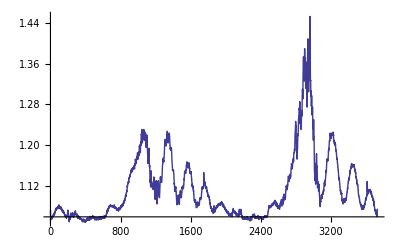
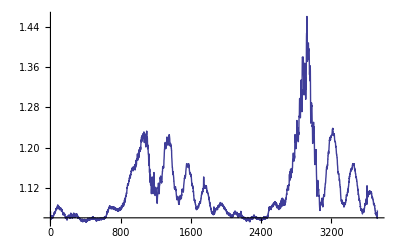
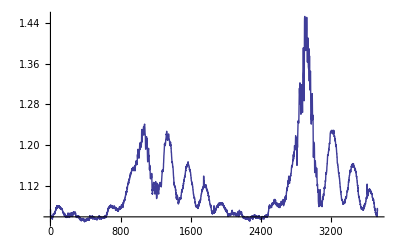
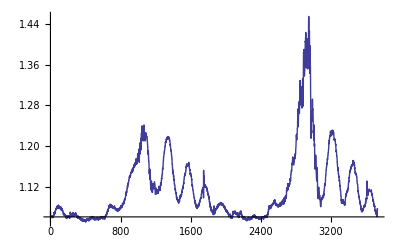
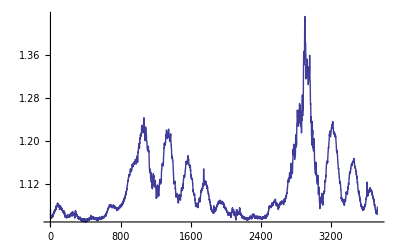
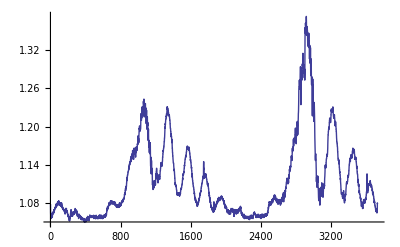
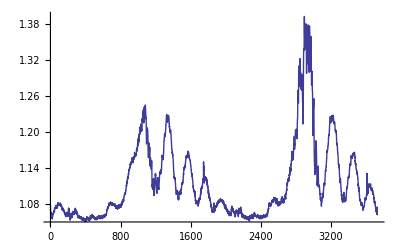
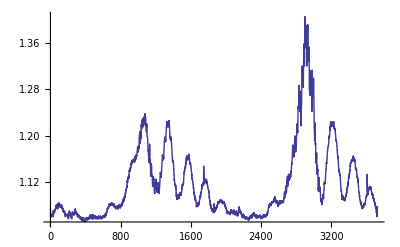

```mathematica
Table[ListLinePlot[cyklus[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]
```

{3729,3728,3730,3730,3729,3729,3729,3728,3729,3727,3729,3728,3728,3728,3728,3728,3729,3730,3729,3730,3729,3729,3730,3730,3730,3731,3730,3729,3729,3729,3728,3729,3729,3728,3729,3729,3729,3729,3730,3728,3730,3729,3728,3729,3728,3727,3728,3727,3728,3728,3729,3729,3728,3728,3729,3728,3729,3728,3729,3729,3729,3729,3731,3731,3730,3731,3729,3730,3730,3729,3729,3730,3729,3729,3730,3730,3729,3729,3730,3730,3731,3729,3730,3729,3730,3731,3730,3730,3731,3729,3729,3729,3729,3729,3729,3729,3729,3731,3729,3729,3730,3728,3729,3728,3729,3728,3727,3728,3729,3728,3729,3729,3730,3730,3730,3730,3728,3730,3730,3729,3729,3728,3728,3728,3727,3728,3727,3728,3728,3728,3728,3728,3728,3727,3727,3728,3728,3728,3729,3728,3729,3729,3730,3729,3730,3730,3730,3730,3730,3730,3730,3732,3731,3731,3732,3731,3732,3731,3730,3730,3729,3729,3728,3729,3728,3727,3727,3727,3727,3727,3726,3727,3727,3728,3728,3728,3728,3729,3728,3729,3729,3730,3730,3730,3732,3731,3731,3730,3731,3730,3731,3730,3730,3729,3729,3728,3728,3727,3727,3728,3729,3731,3730,3731,3730,3731,3730,3729,3730,3730,3729,3728,3728,3729,3729,3729,3729,3730,3729,3730,3730,3730,3731,3731,3730,3731,3730,3730,3729,3730,3727,3728,3726,3727,3727,3727,3728,3728,3728,3728,3729,3728,3728,3728,3728,3729,3729,3729,3729,3728,3728,3729,3730,3730,3729,3729,3731,3730,3729,3730,3731,3729,3729,3730,3729,3729,3728,3729,3729,3728,3729,3729,3730,3729,3729,3730,3729,3728,3729}

```mathematica
pom5=Min[Table[Length[cyklus[[i]]],{i,1,Length[cyklus]}]];
pom6=Table[Take[cyklus[[i]],pom5],{i,1,Length[cyklus]}];
```

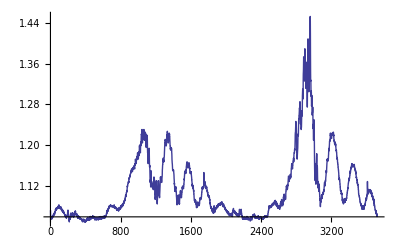
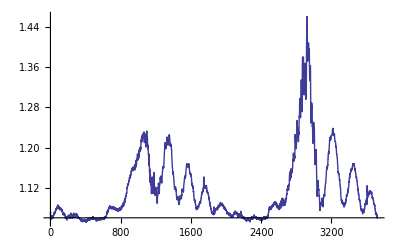
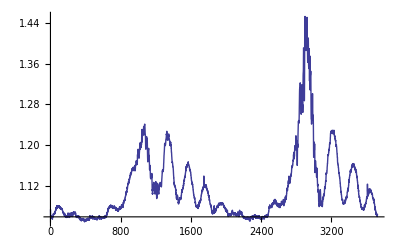
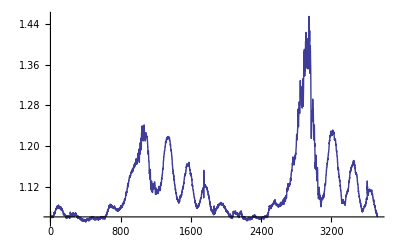
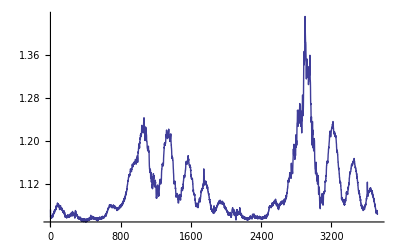
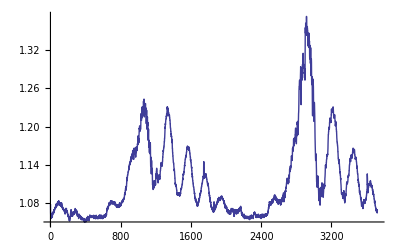
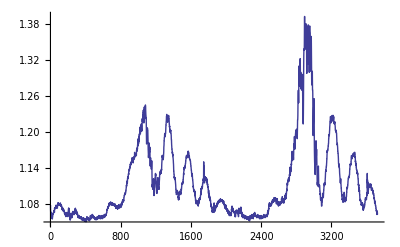
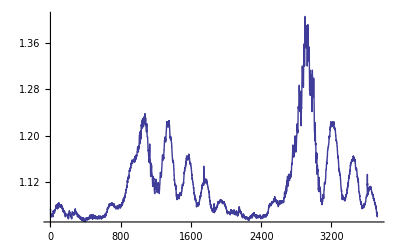

```mathematica
Table[ListLinePlot[pom6[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[pom6]//Dimensions
```

{3726,279}

```mathematica
priemernehodnotydruhystlpec=Table[Mean[pom6[[All,i]]],{i,1,3726}];
```

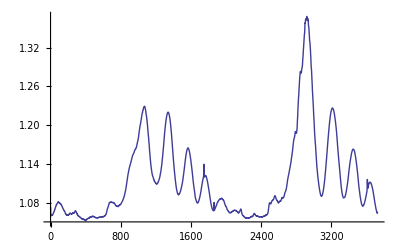

```mathematica
ListLinePlot[priemernehodnotydruhystlpec]
```

```mathematica
cyklus3={};
cyklus4={};
cyklus5={};
Table[AppendTo[cyklus3,tretistlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus4,stvrtystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
Table[AppendTo[cyklus5,piatystlpec[[pom4[[i]];;pom4[[i+2]]]]],{i,2,Length[pom4]-2,2}];
```

```mathematica
cyklus3//Length
```

279

```mathematica
Table[ListLinePlot[cyklus3[[i]],PlotRange->All],{i,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

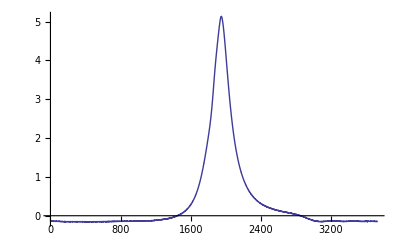
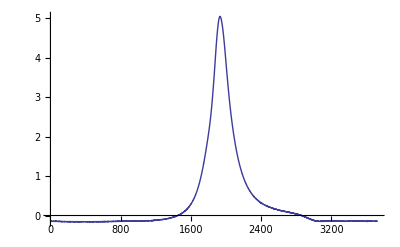
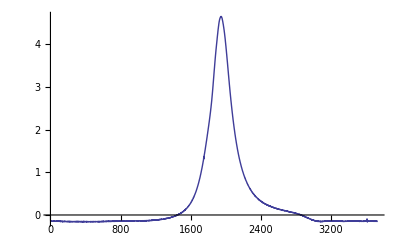
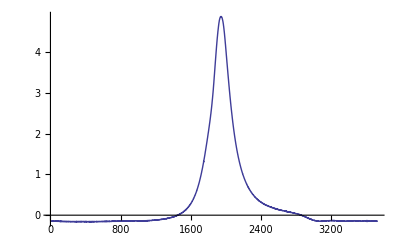
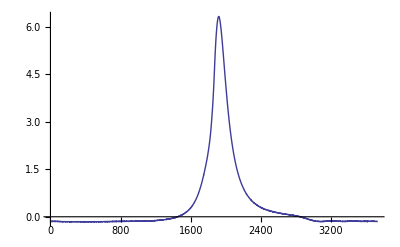
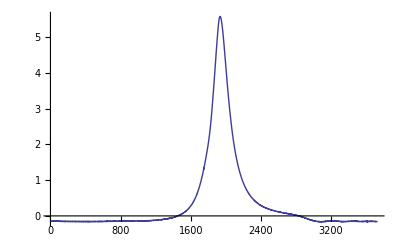
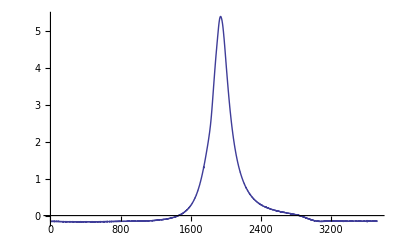
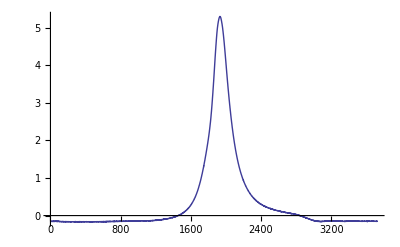

```mathematica
Table[ListLinePlot[cyklus4[[i]],PlotRange->All],{i,1,10}]
```

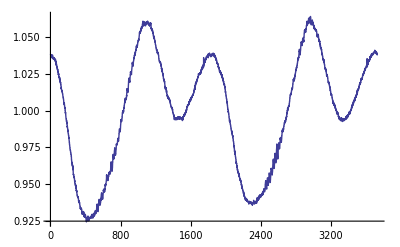
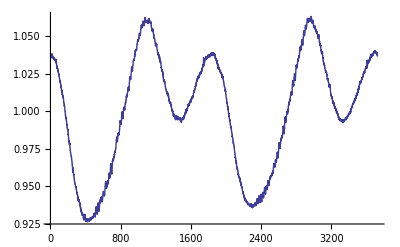
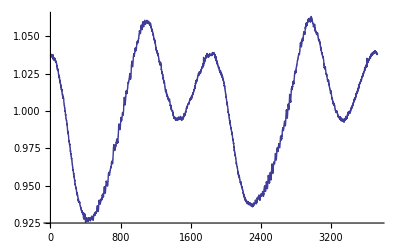
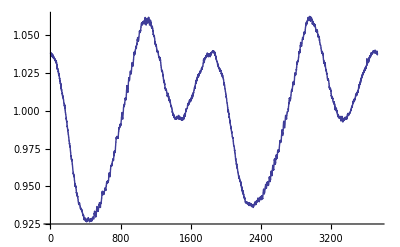
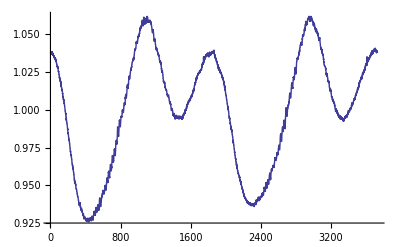
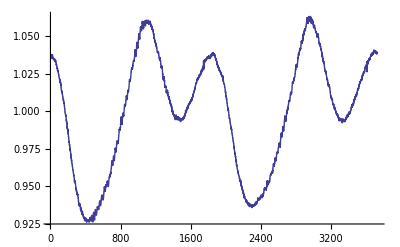
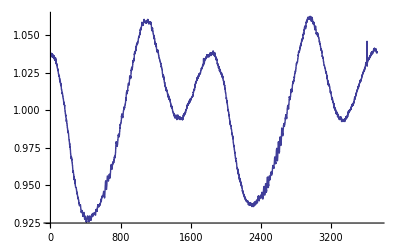
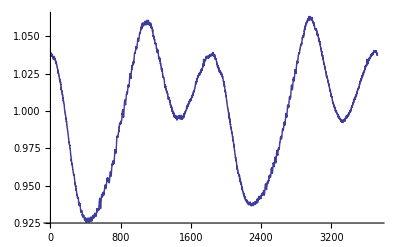

```mathematica
Table[ListLinePlot[cyklus5[[i]],PlotRange->All],{i,1,10}]
```

```mathematica
Table[Length[cyklus3[[i]]],{i,1,Length[cyklus]}]
```

{3729,3728,3730,3730,3729,3729,3729,3728,3729,3727,3729,3728,3728,3728,3728,3728,3729,3730,3729,3730,3729,3729,3730,3730,3730,3731,3730,3729,3729,3729,3728,3729,3729,3728,3729,3729,3729,3729,3730,3728,3730,3729,3728,3729,3728,3727,3728,3727,3728,3728,3729,3729,3728,3728,3729,3728,3729,3728,3729,3729,3729,3729,3731,3731,3730,3731,3729,3730,3730,3729,3729,3730,3729,3729,3730,3730,3729,3729,3730,3730,3731,3729,3730,3729,3730,3731,3730,3730,3731,3729,3729,3729,3729,3729,3729,3729,3729,3731,3729,3729,3730,3728,3729,3728,3729,3728,3727,3728,3729,3728,3729,3729,3730,3730,3730,3730,3728,3730,3730,3729,3729,3728,3728,3728,3727,3728,3727,3728,3728,3728,3728,3728,3728,3727,3727,3728,3728,3728,3729,3728,3729,3729,3730,3729,3730,3730,3730,3730,3730,3730,3730,3732,3731,3731,3732,3731,3732,3731,3730,3730,3729,3729,3728,3729,3728,3727,3727,3727,3727,3727,3726,3727,3727,3728,3728,3728,3728,3729,3728,3729,3729,3730,3730,3730,3732,3731,3731,3730,3731,3730,3731,3730,3730,3729,3729,3728,3728,3727,3727,3728,3729,3731,3730,3731,3730,3731,3730,3729,3730,3730,3729,3728,3728,3729,3729,3729,3729,3730,3729,3730,3730,3730,3731,3731,3730,3731,3730,3730,3729,3730,3727,3728,3726,3727,3727,3727,3728,3728,3728,3728,3729,3728,3728,3728,3728,3729,3729,3729,3729,3728,3728,3729,3730,3730,3729,3729,3731,3730,3729,3730,3731,3729,3729,3730,3729,3729,3728,3729,3729,3728,3729,3729,3730,3729,3729,3730,3729,3728,3729}

```mathematica
pom5=Min[Table[Length[cyklus3[[i]]],{i,1,Length[cyklus3]}]];
cyklus3orezany=Table[Take[cyklus3[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus4orezany=Table[Take[cyklus4[[i]],pom5],{i,1,Length[cyklus3]}];
cyklus5orezany=Table[Take[cyklus5[[i]],pom5],{i,1,Length[cyklus3]}];
```

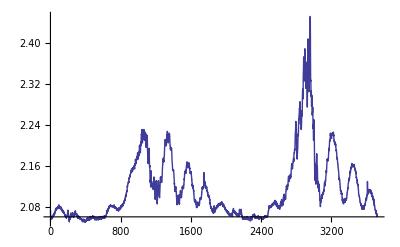
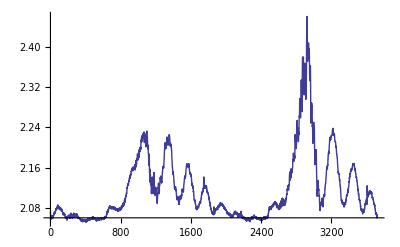
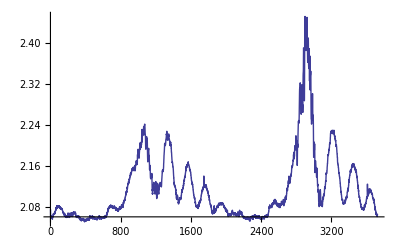
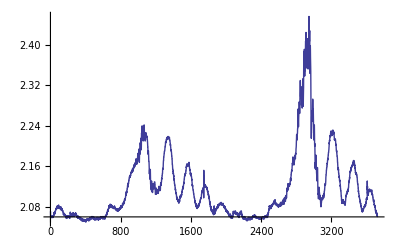
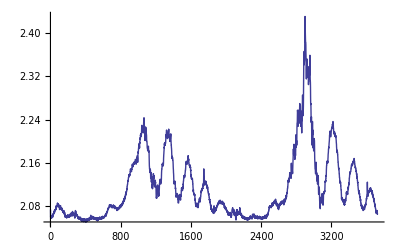
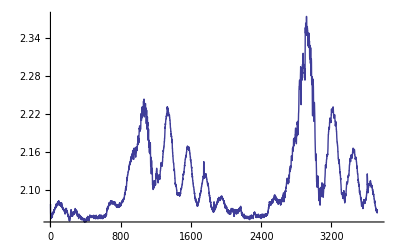
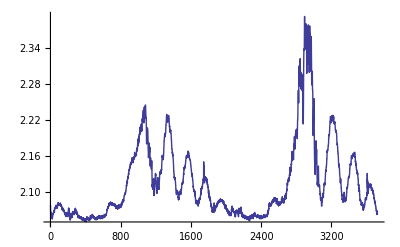
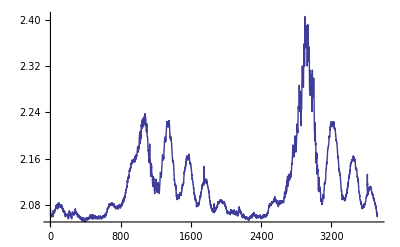

```mathematica
Table[ListLinePlot[cyklus3orezany[[i]]+1,PlotRange->All],{i,1,10}]
```

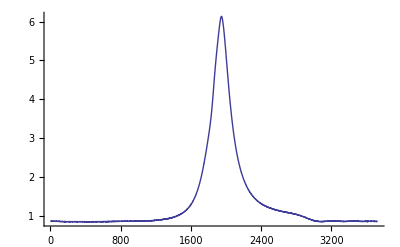
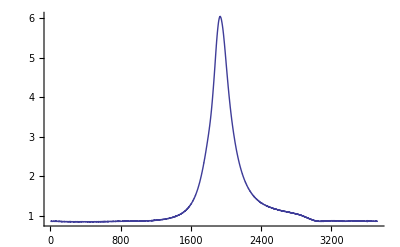
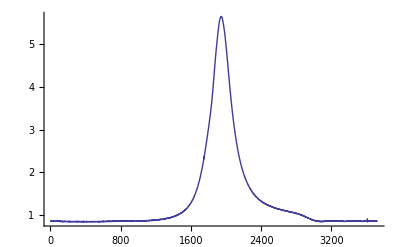
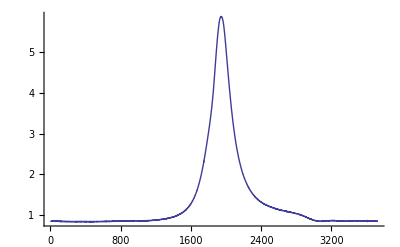
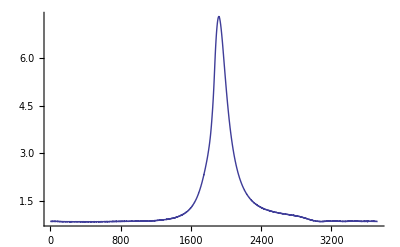
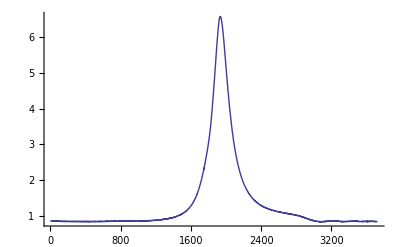
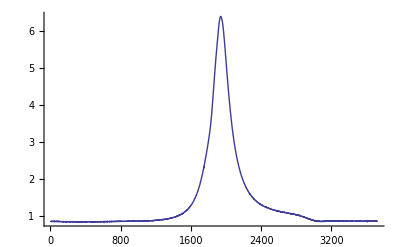
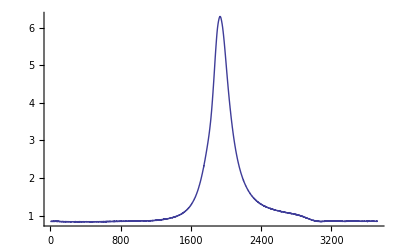

```mathematica
Table[ListLinePlot[cyklus4orezany[[i]]+1,PlotRange->All],{i,1,10}]
```

```mathematica
Transpose[cyklus3orezany]//Dimensions
```

{3726,279}

```mathematica
priemernehodnoty3stlpec=Table[Mean[cyklus3orezany[[All,i]]],{i,1,3726}];
priemernehodnoty4stlpec=Table[Mean[cyklus4orezany[[All,i]]],{i,1,3726}];
priemernehodnoty5stlpec=Table[Mean[cyklus5orezany[[All,i]]],{i,1,3726}];
```

```mathematica
Length[priemernehodnoty4stlpec]
```

3726

```mathematica
k=0;
x=Table[k=k+720/Length[priemernehodnoty4stlpec]//N,{Length[priemernehodnoty4stlpec]}];
```

```mathematica
obr3=ListLinePlot[priemernehodnoty3stlpec]
```

-Graphics-

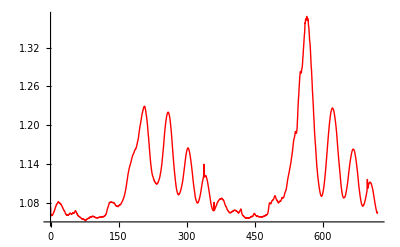

```mathematica
dataobr3=Transpose@{x,priemernehodnoty3stlpec};
obr3a1600=ListLinePlot[dataobr3,PlotStyle->Red]
```

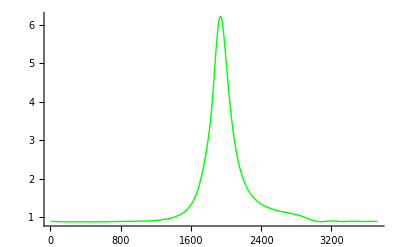

```mathematica
obr4=ListLinePlot[priemernehodnoty4stlpec+1.0335, PlotStyle->Green,PlotRange->All]
priemernehodnoty4stlpecnove=priemernehodnoty4stlpec+1.1335;
```

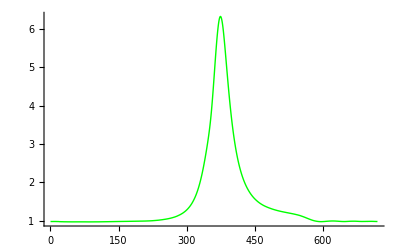

```mathematica
dataobr4=Transpose@{x,priemernehodnoty4stlpecnove};
obr1600va=ListLinePlot[dataobr4,PlotStyle->Green,PlotRange->All]
```

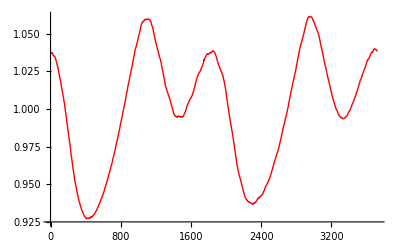

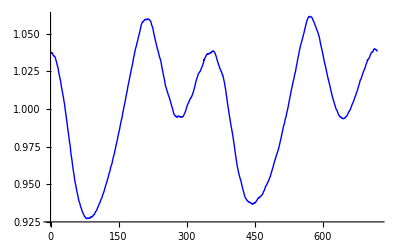

```mathematica
obr5=ListLinePlot[priemernehodnoty5stlpec,PlotStyle->Red]
dataobr5=Transpose@{x,priemernehodnoty5stlpec};
obr1600a=ListLinePlot[dataobr5,PlotStyle->Blue]
```

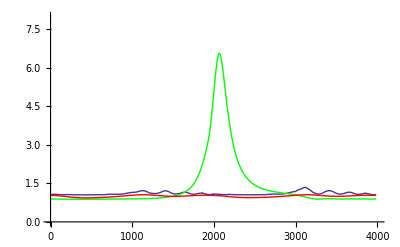

```mathematica
Show[{obr3,obr4,obr5},PlotRange->{{0,4000},{0,8}},AxesOrigin->{0,0}]
```

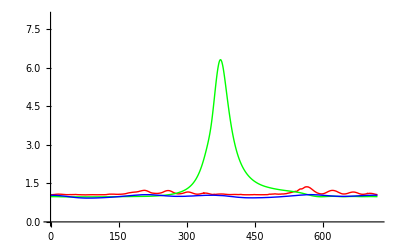

```mathematica
obrfinala=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0,8}},AxesOrigin->{0,0}]
```

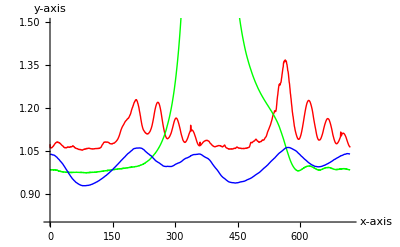

```mathematica
obrfinaladetail=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},LabelStyle->(FontSize->14),AxesLabel->{"x-axis","y-axis"}]
```

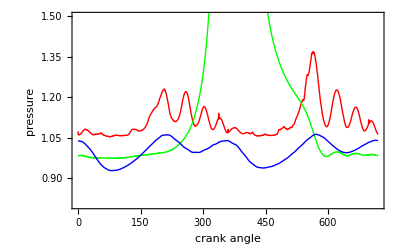

```mathematica
obrfinaladetail=GraphicsGrid[{{obr3a,obr4a,obr5a}},ImageSize->{1000,250}];
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},PlotRange->{{-3,0},{0,1}},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```

```mathematica
Show[{obr3a,obr4a,obr5a},PlotRange->{{0,720},{0.8,1.5}},AxesOrigin->{0,0.8},Frame->True,FrameLabel->{"crank angle","pressure"},LabelStyle->(FontSize->16)]
```

-Graphics-